```mathematica
(* Use Mathematica to compute the derivatives of the fit functions wrt each parameter *)
(* R. Sheehan 19 - 10 - 2021 *)
Clear[η, Id, Is, k, T]
Vd = η k T Log[1+(Id/Is)];
Print["(∂ V)/(∂ SubscriptBox[I, d]) = ",D[Vd,Id]]
Print["(∂ V)/(∂ η) = ",D[Vd,η]]
Print["(∂ V)/(∂ T) = ",D[Vd,T]]
Print["(∂ V)/(∂ SubscriptBox[I, s]) = ",D[Vd,Is]]
```

(∂ V)/(∂ SubscriptBox[I, d]) = (k T η)/((1+Id/Is) Is)

(∂ V)/(∂ η) = k T Log[1+Id/Is]

(∂ V)/(∂ T) = k η Log[1+Id/Is]

(∂ V)/(∂ SubscriptBox[I, s]) = -(Id k T η)/((1+Id/Is) Is^2)

```mathematica
Clear[η, Id, Is, k, T]
Print["Vd = ",Vd/.Id->50/.η->1.5/.T->(273.15+22)/.Is->5×10^-11/.k->8.61733×10^-5]
Print["(∂ V)/(∂ SubscriptBox[I, d]) = ",D[Vd,Id]/.Id->50/.η->1.5/.T->(273.15+22)/.Is->5×10^-11/.k->8.61733×10^-5]
Print["(∂ V)/(∂ η) = ",D[Vd,η]/.Id->50/.η->1.5/.T->(273.15+22)/.Is->5×10^-11/.k->8.61733×10^-5]
Print["(∂ V)/(∂ T) = ",D[Vd,T]/.Id->50/.η->1.5/.T->(273.15+22)/.Is->5×10^-11/.k->8.61733×10^-5]
Print["(∂ V)/(∂ SubscriptBox[I, s]) = ",D[Vd,Is]/.Id->50/.η->1.5/.T->(273.15+22)/.Is->5×10^-11/.k->8.61733×10^-5]
```

Vd = 1.05415

(∂ V)/(∂ SubscriptBox[I, d]) = 0.000763021

(∂ V)/(∂ η) = 0.702769

(∂ V)/(∂ T) = 0.00357158

(∂ V)/(∂ SubscriptBox[I, s]) = -7.63021×10^8

0.727721

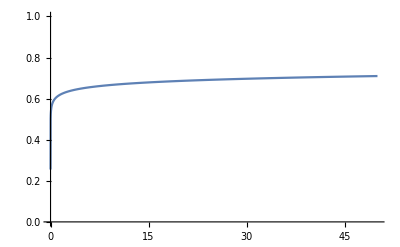

```mathematica
η=1; (* Ideality *)
T = 273.15+25; (* Temperature in K *)
k=8.61733×10^-5; (* Physical constants in J / C K *)
Is = 5000×10^-14; (* Saturation Current in mA *)
Vd/.Id->100
Plot[Vd,{Id,-0, 50},PlotRange->{{0,50},{-0,1}}]
```

```mathematica
(* Diode equation with series resistance *)
(* R. Sheehan 7 - 4 - 2022 *)
Clear[η, Id, Is, k, T, Rs]
VdR = η k T Log[1+(Id/Is)]+Rs Id;
Print["(∂ V)/(∂ SubscriptBox[I, d]) = ",D[VdR,Id]]
Print["(∂ V)/(∂ η) = ",D[VdR,η]]
Print["(∂ V)/(∂ T) = ",D[VdR,T]]
Print["(∂ V)/(∂ SubscriptBox[I, s]) = ",D[VdR,Is]]
Print["(∂ V)/(∂ SubscriptBox[R, s]) = ",D[VdR,Rs]]
```

(∂ V)/(∂ SubscriptBox[I, d]) = Rs+(k T η)/((1+Id/Is) Is)

(∂ V)/(∂ η) = k T Log[1+Id/Is]

(∂ V)/(∂ T) = k η Log[1+Id/Is]

(∂ V)/(∂ SubscriptBox[I, s]) = -(Id k T η)/((1+Id/Is) Is^2)

(∂ V)/(∂ SubscriptBox[R, s]) = Id

```mathematica
Clear[η, Id, Is, k, T, Rs]
Print["Vd = ",VdR/.Id->50/.η->1.5/.T->(273.15+22)/.Is->5×10^-11/.k->8.61733×10^-5/.Rs->(10.0/1000.0)]
Print["(∂ V)/(∂ SubscriptBox[I, d]) = ",D[VdR,Id]/.Id->50/.η->1.5/.T->(273.15+22)/.Is->5×10^-11/.k->8.61733×10^-5/.Rs->(10.0/1000.0)]
Print["(∂ V)/(∂ η) = ",D[VdR,η]/.Id->50/.η->1.5/.T->(273.15+22)/.Is->5×10^-11/.k->8.61733×10^-5/.Rs->(10.0/1000.0)]
Print["(∂ V)/(∂ T) = ",D[VdR,T]/.Id->50/.η->1.5/.T->(273.15+22)/.Is->5×10^-11/.k->8.61733×10^-5/.Rs->(10.0/1000.0)]
Print["(∂ V)/(∂ SubscriptBox[I, s]) = ",D[VdR,Is]/.Id->50/.η->1.5/.T->(273.15+22)/.Is->5×10^-11/.k->8.61733×10^-5/.Rs->(10.0/1000.0)]
Print["(∂ V)/(∂ SubscriptBox[R, s]) = ",D[VdR,Rs]/.Id->50/.η->1.5/.T->(273.15+22)/.Is->5×10^-11/.k->8.61733×10^-5/.Rs->(10.0/1000.0)]
```

Vd = 1.55415

(∂ V)/(∂ SubscriptBox[I, d]) = 0.010763

(∂ V)/(∂ η) = 0.702769

(∂ V)/(∂ T) = 0.00357158

(∂ V)/(∂ SubscriptBox[I, s]) = -7.63021×10^8

(∂ V)/(∂ SubscriptBox[R, s]) = 50

```mathematica
-0.000458902*1000
```

-0.458902

```mathematica
273.15-158.863
```

114.287

```mathematica
η=1; (* Ideality *)
T = 273.15+25; (* Temperature in K *)
k=8.61733×10^-5; (* Physical constants in J / C K *)
Is = 5000×10^-14; (* Saturation Current in mA *)
Rs = 5.0/1000.0; (* Series Resistance in kΩ *)
Vd/.Id->100
VdR/.Id->100
N[η k T]
N[100/Is]
Plot[{Vd,VdR},{Id,0.5, 50},PlotRange->{{0,50},{0,2}}]
```

Vd

100 c3+c1 Log[1+100 c2]

0.0256926

2.×10^12

-Graphics-

```mathematica
N[0.05Log[100/10^-11]]
```

1.49668

```mathematica
N[0.05Log[1+100×10^10]+(0.5/1000.0)*100]
```

1.43155

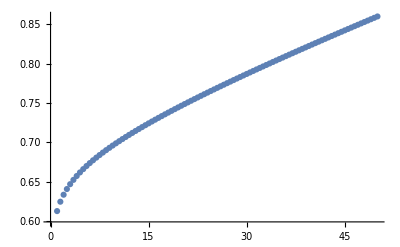

0.0717262 Log[1+2099.71 x]

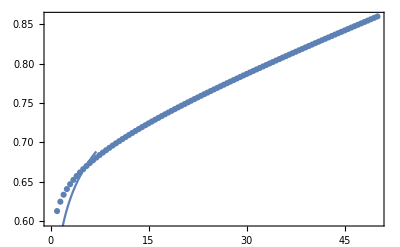

```mathematica
(* Can't seem to get a decent fit for the diode with my own method *)
(* Try Mathematica's Own NonLinear Fit Function *)
data=Table[{i,VdR/.Id->i/.η->1.5/.T->(273.15+22)/.Is->5×10^-11/.k->8.61733×10^-5/.Rs->(1.0/1000.0)},{i,1,50,0.5}];
ListPlot[data]
nlm=NonlinearModelFit[data,a Log[1 +b x],{a,b,d},x];
Normal[nlm]
Show[ListPlot[data],Plot[nlm[x],{x,0,7}],Frame->True]
```

```mathematica
N[1.0/2099]
```

0.000476417

```mathematica
(* Diode equation with series resistance *)
(* Simpler model *)
(* R. Sheehan 7 - 4 - 2022 *)
Clear[c1, c2, c3]
VdR = c1 Log[1+c2 Id]+c3 Id;
Print["(∂ V)/(∂ SubscriptBox[I, d]) = ",D[VdR,Id]]
Print["(∂ V)/(∂ c1) = ",D[VdR,c1]]
Print["(∂ V)/(∂ c2) = ",D[VdR,c2]]
Print["(∂ V)/(∂ c3) = ",D[VdR,c3]]
```

(∂ V)/(∂ SubscriptBox[I, d]) = c3+(c1 c2)/(1+c2 Id)

(∂ V)/(∂ c1) = Log[1+c2 Id]

(∂ V)/(∂ c2) = (c1 Id)/(1+c2 Id)

(∂ V)/(∂ c3) = Id

```mathematica
Clear[c1, c2, c3]
Print["Vd = ",VdR/.Id->50/.c1->0.03/.c2->(1.0/(5×10^-11))/.c3->(10.0/1000.0)]
Print["(∂ V)/(∂ SubscriptBox[I, d]) = ",D[VdR,Id]/.Id->50/.c1->0.03/.c2->(1.0/(5×10^-11))/.c3->(10.0/1000.0)]
Print["(∂ V)/(∂ c1) = ",D[VdR,c1]/.Id->50/.c1->0.03/.c2->(1.0/(5×10^-11))/.c3->(10.0/1000.0)]
Print["(∂ V)/(∂ c2) = ",D[VdR,c2]/.Id->50/.c1->0.03/.c2->(1.0/(5×10^-11))/.c3->(10.0/1000.0)]
Print["(∂ V)/(∂ c3) = ",D[VdR,c3]/.Id->50/.c1->0.03/.c2->(1.0/(5×10^-11))/.c3->(10.0/1000.0)]
```

Vd = 1.32893

(∂ V)/(∂ SubscriptBox[I, d]) = 0.0106

(∂ V)/(∂ c1) = 27.631

(∂ V)/(∂ c2) = 1.5×10^-12

(∂ V)/(∂ c3) = 50

```mathematica
N[Log[1.0+(50.0/(5.0×10^-11))]]
```

27.631

```mathematica
N[1/(5.0×10^-11)]
```

2.×10^10

```mathematica
2.0
```

```mathematica
N[1.0+(50.0/(5.0×10^-11))]
```

1.×10^12

```mathematica
(* look at the Lorentzian function *)
(* R. Sheehan 20 - 10 - 2021 *)
Clear[x0,Γ];
L=(Γ/2)/((x-x0)^2+(Γ/2)^2);
D[L,x]
D[L, x0]
D[L,Γ]
```

-((x-x0) Γ)/(((x-x0)^2+Γ^2/4)^2)

((x-x0) Γ)/(((x-x0)^2+Γ^2/4)^2)

-Γ^2/(4 ((x-x0)^2+Γ^2/4)^2)+1/(2 ((x-x0)^2+Γ^2/4))

```mathematica
Lor[x_,A_,x0_,G_]:=A G/((x-x0)^2+(G)^2);
```

```mathematica
Solve[D[Lor[x,A,x0,g],x]==0,x]
```

{{x→x0}}

```mathematica
Lor[x0,A,x0,G]
```

A/G

```mathematica
D[Lor[x,A,x0,G],x]
```

-(2 A G (x-x0))/((G^2+(x-x0)^2)^2)

```mathematica
D[Lor[x,A,x0,G],x0]
```

(2 A G (x-x0))/((G^2+(x-x0)^2)^2)

```mathematica
D[Lor[x,A,x0,G],G]
```

-(2 A G^2)/((G^2+(x-x0)^2)^2)+A/(G^2+(x-x0)^2)

```mathematica
D[Lor[x,A,x0,G],A]
```

G/(G^2+(x-x0)^2)

```mathematica
Lor[80,80,2.5]//N
```

0.8

```mathematica
D[Lor[x,x0,g],g]
```

-(2 g^2)/((g^2+(x-x0)^2)^2)+1/(g^2+(x-x0)^2)

```mathematica
Clear[x0,g];
D[Lor[x,x0,g],x0]/.x->80/.x0->80/.g->1
D[Lor[x,x0,g],g]/.x->80/.x0->80/.g->1
```

0

-1

```mathematica
D[Lor[x,x0,g],g]
```

-(2 g^2)/((g^2+(x-x0)^2)^2)+1/(g^2+(x-x0)^2)

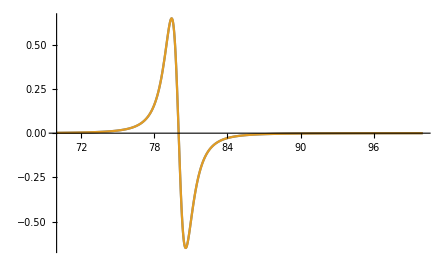

```mathematica
x0=80;
g=1;
Plot[{-((x-x0) g)/(((x-x0)^2+g^2/4)^2),-4 (x-x0)1/g(Lor[x,x0,g])^2},{x,xl,xh},PlotRange->{{xl,xh},All}]
```

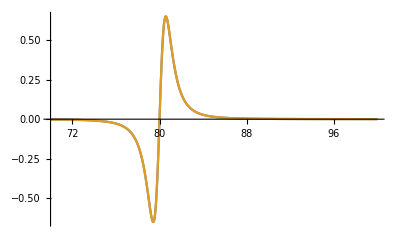

```mathematica
x0=80;
g=2;
Plot[{((x-x0) g)/(((x-x0)^2+g^2/4)^2),4 (x-x0)1/g(Lor[x,x0,g])^2},{x,xl,xh},PlotRange->{{xl,xh},All}]
```

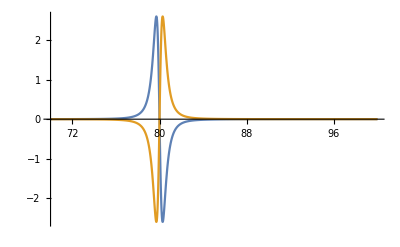

```mathematica
x0=80;
g=1;
Plot[{-4 (x-x0)1/g(Lor[x,x0,g])^2,4 (x-x0)1/g(Lor[x,x0,g])^2},{x,xl,xh},PlotRange->{{xl,xh},All}]
```

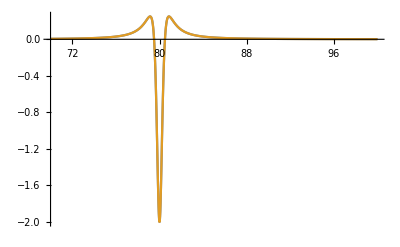

```mathematica
x0=80;
g=1;
Plot[{-g^2/(4  ((x-x0)^2+g^2/4)^2)+1/(2  ((x-x0)^2+g^2/4)),Lor[x,x0,g]/g- (Lor[x,x0,g])^2},{x,xl,xh},PlotRange->{{xl,xh},All}]
```

```mathematica
Gauss[x_, a_, b_, c_]:=a Exp[-(x-b)^2/(2 c^2)];
```

```mathematica
D[Gauss[x, a, b, c],x]
```

-(a ⅇ^(-(-b+x)^2/(2 c^2)) (-b+x))/c^2

```mathematica
D[Gauss[x, a, b, c],a]
```

ⅇ^(-(-b+x)^2/(2 c^2))

```mathematica
D[Gauss[x, a, b, c],b]
```

(a ⅇ^(-(-b+x)^2/(2 c^2)) (-b+x))/c^2

```mathematica
D[Gauss[x, a, b, c],c]
```

(a ⅇ^(-(-b+x)^2/(2 c^2)) (-b+x)^2)/c^3

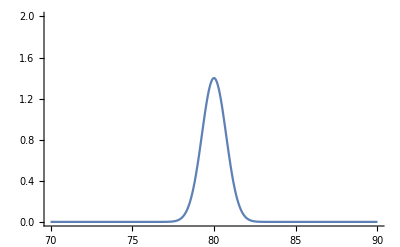

```mathematica
a=1.4;
b=80;
c=0.74;
Plot[Gauss[x, a, b, c],{x,70,90},PlotRange->{All,{0,2}}]
```

```mathematica
Print["FWHM = ",2.0 √(2.0 Log[2]) c]
Print["HWHM = ",√(2.0 Log[2]) c]
```

FWHM = 1.74257

HWHM = 0.871283

```mathematica
f=82;
Gauss[x, a, b, c]/.x->f//N
1/a Gauss[x, a, b, c]/.x->f//N
(x-b)/c^2 Gauss[x, a, b, c]/.x->f//N
(x-b)^2/c^3 Gauss[x, a, b, c]/.x->f//N
```

0.036304

0.0259314

0.132593

0.358359

```mathematica
Exp[-3.65]
```

0.0259911

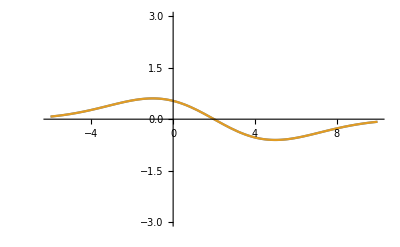

```mathematica
a=3;
b=2;
c=3;
Plot[{-(a ⅇ^(-(-b+x)^2/(2 c^2)) (-b+x))/c^2,-(x-b)/c^2 Gauss[x, a, b, c]},{x,-6,10},PlotRange->{All,{-3,3}}]
```

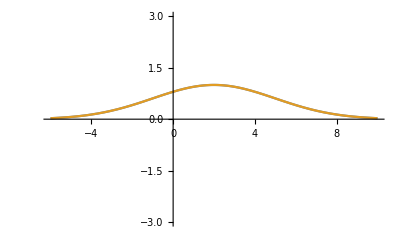

```mathematica
a=3;
b=2;
c=3;
Plot[{ⅇ^(-(-b+x)^2/(2 c^2)),1/a Gauss[x, a, b, c]},{x,-6,10},PlotRange->{All,{-3,3}}]
```

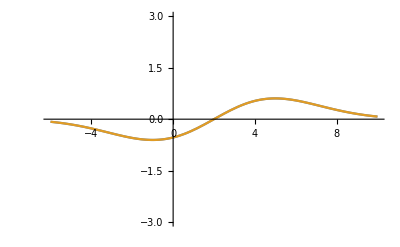

```mathematica
a=3;
b=2;
c=3;
Plot[{(a ⅇ^(-(-b+x)^2/(2 c^2)) (-b+x))/c^2,(x-b)/c^2 Gauss[x, a, b, c]},{x,-6,10},PlotRange->{All,{-3,3}}]
```

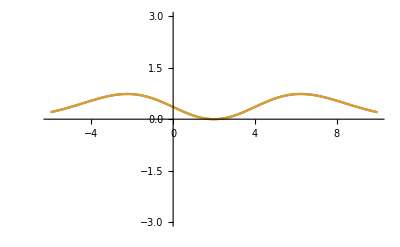

```mathematica
a=3;
b=2;
c=3;
Plot[{(a ⅇ^(-(-b+x)^2/(2 c^2)) (-b+x)^2)/c^3,(x-b)^2/c^3 Gauss[x, a, b, c]},{x,-6,10},PlotRange->{All,{-3,3}}]
```

```mathematica
zz=(x-x0+ⅈ γ)/σ;
Print["(∂ z)/(∂ x) = ",D[zz,x]];
Print["(∂ z)/(∂ x0) = ",D[zz,x0]];
Print["(∂ z)/(∂ γ) = ",D[zz,γ]];
Print["(∂ z)/(∂ σ) = ",D[zz,σ]];
```

(∂ z)/(∂ x) = 1/σ

(∂ z)/(∂ x0) = -1/σ

(∂ z)/(∂ γ) = ⅈ/σ

(∂ z)/(∂ σ) = -(x-x0+ⅈ γ)/σ^2

```mathematica
Clear[x,x0,h,g,γ]
Faddeeva[z_]:=ⅇ^(-z^2) Erfc[-ⅈ z];
Gauss[x_,aa_,bb_,cc_]:=aa Exp[-(x-bb)^2/(2 cc^2)];
Lorentz[x_,aa_,bb_,cc_]:=aa cc/((x-bb)^2+cc^2);
Voigt[x_,h_,g_,σ_,x0_]:=Module[
{z,ret},
z=(x-x0+ⅈ g)(1/σ);
ret=h Faddeeva[z];
Return[ret]
];

Print["(∂ V)/(∂ h) = ",D[Voigt[x,h,γ,σ,x0],h]];
Print["(∂ V)/(∂ x) = ",D[Voigt[x,h,γ,σ,x0],x]];
Print["(∂ V)/(∂ SubscriptBox[x, 0]) = ",D[Voigt[x,h,γ,σ,x0],x0]];
Print["(∂ V)/(∂ g) = ",D[Voigt[x,h,γ,σ,x0],γ]];
Print["(∂ V)/(∂ σ) = ",D[Voigt[x,h,γ,σ,x0],σ]];
```

(∂ V)/(∂ h) = ⅇ^(-(x-x0+ⅈ γ)^2/σ^2) Erfc[-(ⅈ (x-x0+ⅈ γ))/σ]

(∂ V)/(∂ x) = (2 ⅈ h)/(√π σ)-(2 ⅇ^(-(x-x0+ⅈ γ)^2/σ^2) h (x-x0+ⅈ γ) Erfc[-(ⅈ (x-x0+ⅈ γ))/σ])/σ^2

(∂ V)/(∂ SubscriptBox[x, 0]) = -(2 ⅈ h)/(√π σ)+(2 ⅇ^(-(x-x0+ⅈ γ)^2/σ^2) h (x-x0+ⅈ γ) Erfc[-(ⅈ (x-x0+ⅈ γ))/σ])/σ^2

(∂ V)/(∂ g) = -(2 h)/(√π σ)-(2 ⅈ ⅇ^(-(x-x0+ⅈ γ)^2/σ^2) h (x-x0+ⅈ γ) Erfc[-(ⅈ (x-x0+ⅈ γ))/σ])/σ^2

(∂ V)/(∂ σ) = -(2 ⅈ h (x-x0+ⅈ γ))/(√π σ^2)+(2 ⅇ^(-(x-x0+ⅈ γ)^2/σ^2) h (x-x0+ⅈ γ)^2 Erfc[-(ⅈ (x-x0+ⅈ γ))/σ])/σ^3

```mathematica
Print["Values of the Voigt Function and its Derivatives"]
Print["V = ",Voigt[x,h,γ,σ,x0]/.{x->81,h->2,γ->1,σ->1,x0->80}];
Print["(∂ V)/(∂ h) = ",D[Voigt[x,h,γ,σ,x0],h]/.{x->81,h->2,γ->1,σ->1,x0->80}];
Print["(∂ V)/(∂ x) = ",D[Voigt[x,h,γ,σ,x0],x]/.{x->81,h->2,γ->1,σ->1,x0->80}];
Print["(∂ V)/(∂ SubscriptBox[x, 0]) = ",D[Voigt[x,h,γ,σ,x0],x0]/.{x->81,h->2,γ->1,σ->1,x0->80}];
Print["(∂ V)/(∂ γ) = ",D[Voigt[x,h,γ,σ,x0],γ]/.{x->81,h->2,γ->1,σ->1,x0->80}];
Print["(∂ V)/(∂ σ) = ",D[Voigt[x,h,γ,σ,x0],σ]/.{x->81,h->2,γ->1,σ->1,x0->80}];
```

Values of the Voigt Function and its Derivatives

V = 2 ⅇ^(-2 ⅈ) Erfc[1-ⅈ]

(∂ V)/(∂ h) = ⅇ^(-2 ⅈ) Erfc[1-ⅈ]

(∂ V)/(∂ x) = (4 ⅈ)/(√π)-(4+4 ⅈ) ⅇ^(-2 ⅈ) Erfc[1-ⅈ]

(∂ V)/(∂ SubscriptBox[x, 0]) = -(4 ⅈ)/(√π)+(4+4 ⅈ) ⅇ^(-2 ⅈ) Erfc[1-ⅈ]

(∂ V)/(∂ γ) = -4/(√π)+(4-4 ⅈ) ⅇ^(-2 ⅈ) Erfc[1-ⅈ]

(∂ V)/(∂ σ) = (4-4 ⅈ)/(√π)+8 ⅈ ⅇ^(-2 ⅈ) Erfc[1-ⅈ]

```mathematica
Print["Max of the Voigt Function"]
Clear[x,x0,h,g,γ]
Print["V_max = ",Voigt[x0,h,γ,σ,x0]];
```

Max of the Voigt Function

V_max = ⅇ^(γ^2/σ^2) h Erfc[γ/σ]

```mathematica
Solve[Voigt[x,h,γ,σ,x0]==Voigt[x0,h,γ,σ,x0],x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[ⅇ^(-(x-x0+ⅈ γ)^2/σ^2) h Erfc[-(ⅈ (x-x0+ⅈ γ))/σ]==ⅇ^(γ^2/σ^2) h Erfc[γ/σ],x]

```mathematica
x0=80;
(*h=2.28256;
γ=1.14966;
σ=1.81328;*)
h=27.9483;
γ=0.606449;
σ=2.52756;
Vmax=Voigt[x0,h,γ,σ,x0];
Print["Vmax = ",Vmax]
root=Re[FindRoot[Re[Voigt[x,h,γ,σ,x0]]==Vmax/2,{x,83}]⟦1,2⟧];
c2=Abs[root-x0];
Print["root = ",root]
Print["HWHM = ",c2];
root=Re[FindRoot[Re[Voigt[x,h,γ,σ,x0]]==Vmax/2,{x,75}]⟦1,2⟧];
c3=Abs[root-x0];
Print["root = ",root]
Print["HWHM = ",c3];
c1=(1.0692γ+√(0.866639 γ^2+4 σ^2))/2;
Print["c1 = ",c1]
```

Vmax = 21.7406+0. ⅈ

root = 82.4468

HWHM = 2.4468

root = 82.4468

HWHM = 2.4468

c1 = 2.86748

```mathematica
c2/c1
```

0.884598

```mathematica
1/(√π)//N
```

0.56419

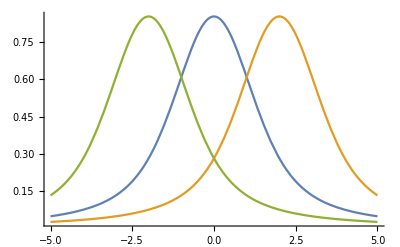

```mathematica
h=2; 
g=1; 
γ=1;
x0=0;
Plot[{Re[Voigt[x,h,g,γ,x0]],Re[Voigt[x,h,g,γ,2]],Re[Voigt[x,h,g,γ,-2]]},{x,-5,5},PlotRange->{All,All}]
```

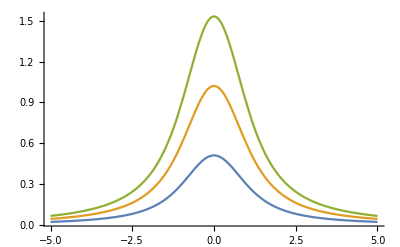

```mathematica
h=2; 
g=1; 
γ=0.5;
x0=0;
Plot[{Re[Voigt[x,h,g,γ,x0]],Re[Voigt[x,2h,g,γ,x0]],Re[Voigt[x,3h,g,γ,x0]]},{x,-5,5},PlotRange->{All,All}]
```

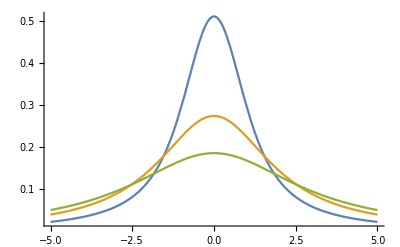

```mathematica
h=2; 
g=1; 
γ=0.5;
x0=0;
Plot[{Re[Voigt[x,h,g,γ,x0]],Re[Voigt[x,h,2g,γ,x0]],Re[Voigt[x,h,3g,γ,x0]]},{x,-5,5},PlotRange->{All,All}]
```

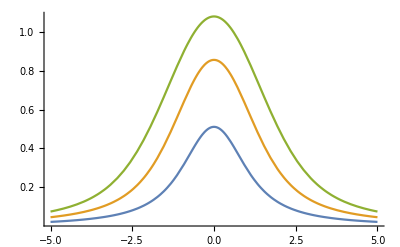

```mathematica
h=2; 
g=1; 
γ=0.5;
x0=0;
Plot[{Re[Voigt[x,h,g,γ,x0]],Re[Voigt[x,h,g,2γ,x0]],Re[Voigt[x,h,g,3γ,x0]]},{x,-5,5},PlotRange->{All,All}]
```

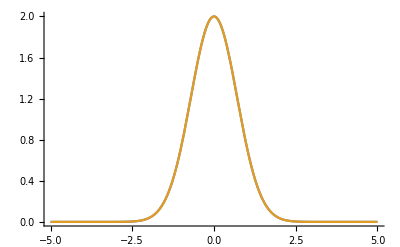

```mathematica
h=2; 
g=0; 
γ=1;
x0=0;
Plot[{Re[Voigt[x,h,g,γ,x0]],Gauss[x,h,x0,γ/(√2)]},{x,-5,5},PlotRange->{All,All}]
```

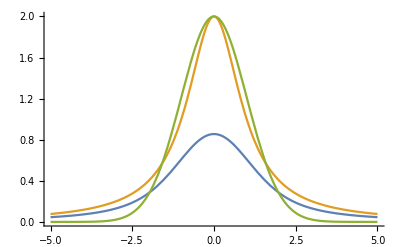

```mathematica
h=2; 
g=1; 
γ=1;
x0=0;
Plot[{Re[Voigt[x,h,g,γ,x0]],Lorentz[x,h,x0,g],Gauss[x,h,x0,γ]},{x,-5,5},PlotRange->{All,All}]
```

```mathematica
Clear[x0,h,g,γ]
Limit[Voigt[x,h,g,γ,x0],γ->0.1]
```

ⅇ^(-100. (ⅈ g+x-x0)^2) h Erfc[(0.-10. ⅈ) (ⅈ g+x-x0)]

```mathematica
Clear[x0,h,g,γ]
D[Voigt[x,h,g,γ,x0],x]
```

(2 ⅈ h)/(√π γ)-(2 ⅇ^(-(ⅈ g+x-x0)^2/γ^2) h (ⅈ g+x-x0) Erfc[-(ⅈ (ⅈ g+x-x0))/γ])/γ^2

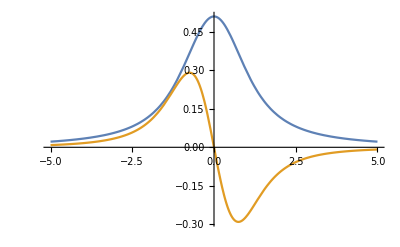

```mathematica
h=2; 
g=1; 
γ=0.5;
x0=0;Plot[{Re[Voigt[x,h,g,γ,x0]],Re[(2 ⅈ h)/(√π γ)-(2 ⅇ^(-(ⅈ g+x-x0)^2/γ^2) h (ⅈ g+x-x0) Erfc[-(ⅈ (ⅈ g+x-x0))/γ])/γ^2]},{x,-5,5}]
```

```mathematica
Clear[x0,h,g,γ]
D[Voigt[x,h,g,γ,x0],x0]
```

-(2 ⅈ h)/(√π γ)+(2 ⅇ^(-(ⅈ g+x-x0)^2/γ^2) h (ⅈ g+x-x0) Erfc[-(ⅈ (ⅈ g+x-x0))/γ])/γ^2

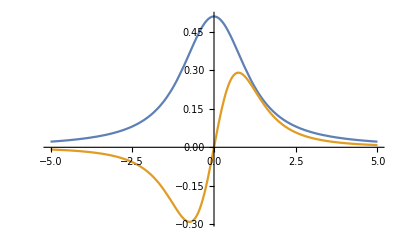

```mathematica
h=2; 
g=1; 
γ=0.5;
x0=0;Plot[{Re[Voigt[x,h,g,γ,x0]],Re[-(2 ⅈ h)/(√π γ)+(2 ⅇ^(-(ⅈ g+x-x0)^2/γ^2) h (ⅈ g+x-x0) Erfc[-(ⅈ (ⅈ g+x-x0))/γ])/γ^2]},{x,-5,5}]
```

```mathematica
Clear[x0,h,g,γ]
D[Voigt[x,h,g,γ,x0],h]
```

ⅇ^(-(ⅈ g+x-x0)^2/γ^2) Erfc[-(ⅈ (ⅈ g+x-x0))/γ]

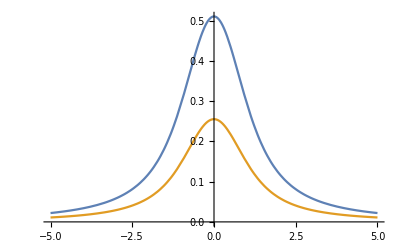

```mathematica
h=2; 
g=1; 
γ=0.5;
x0=0;Plot[{Re[Voigt[x,h,g,γ,x0]],Re[ⅇ^(-(ⅈ g+x-x0)^2/γ^2) Erfc[-(ⅈ (ⅈ g+x-x0))/γ]]},{x,-5,5}]
```

```mathematica
Clear[x0,h,g,γ]
D[Voigt[x,h,g,γ,x0],g]
```

-(2 h)/(√π γ)-(2 ⅈ ⅇ^(-(ⅈ g+x-x0)^2/γ^2) h (ⅈ g+x-x0) Erfc[-(ⅈ (ⅈ g+x-x0))/γ])/γ^2

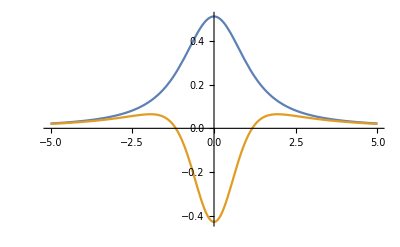

```mathematica
h=2; 
g=1; 
γ=0.5;
x0=0;Plot[{Re[Voigt[x,h,g,γ,x0]],Re[-(2 h)/(√π γ)-(2 ⅈ ⅇ^(-(ⅈ g+x-x0)^2/γ^2) h (ⅈ g+x-x0) Erfc[-(ⅈ (ⅈ g+x-x0))/γ])/γ^2]},{x,-5,5},PlotRange->{All,All}]
```

```mathematica
Clear[x0,h,g,γ]
D[Voigt[x,h,g,γ,x0],γ]
```

-(2 ⅈ h (ⅈ g+x-x0))/(√π γ^2)+(2 ⅇ^(-(ⅈ g+x-x0)^2/γ^2) h (ⅈ g+x-x0)^2 Erfc[-(ⅈ (ⅈ g+x-x0))/γ])/γ^3

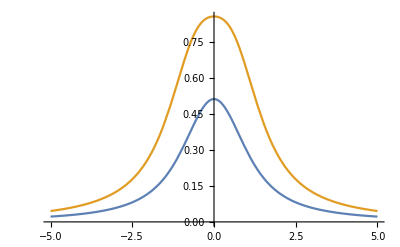

```mathematica
h=2; 
g=1; 
γ=0.5;
x0=0;Plot[{Re[Voigt[x,h,g,γ,x0]],Re[-(2 ⅈ h (ⅈ g+x-x0))/(√π γ^2)+(2 ⅇ^(-(ⅈ g+x-x0)^2/γ^2) h (ⅈ g+x-x0)^2 Erfc[-(ⅈ (ⅈ g+x-x0))/γ])/γ^3]},{x,-5,5}]
```

```mathematica
N[2 √Log[2]]
```

1.66511

```mathematica
N[2 √Log10[2]]
```

1.09732

```mathematica
N[2 √(2Log[2])]
```

2.35482

```mathematica
(*Gauss[x_,aa_,bb_,cc_]:=aa Exp[-(x-bb)^2/(2 cc^2)];*)
Print[Gauss[bb,aa,bb,cc]]
Print[Gauss[bb-√(2 Log[2])cc,aa,bb,cc]]
```

aa

aa/2

```mathematica
Limit[Gauss[bb,aa,bb,cc],cc->0]
```

aa

```mathematica
Gauss[bb,aa,bb,cc]/.cc->0
```

aa

```mathematica
(* Fixed Point Iteration *)
(* Perform iteration Subscript[x, n+1] = g(Subscript[x, n]), where g(x) = x - α f(x), to solve f(x) = 0 *)
(* α is tuning factor to accelerate convergence *)
(* R. Sheehan 1 - 12 - 2021 *)
FPI[f_,x0_,α_,tol_,maxit_]:=Module[
{xnew,xold,dx,count},
count=0;
xold=x0;
While[count<maxit,
xnew=N[xold-α f[xold]];
dx=N[xnew-xold];
If[Abs[dx]<tol,
Print["FPI has converged to a root of f to within tolerance of ",tol," after ",count," iterations"];
Break[];,
Print["Iteration: ",count,", root = ",xnew];
xold=xnew; 
];
count++;
];
Return[xnew]; 
];
```

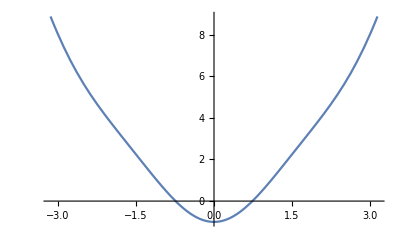

{x→0.739085}

```mathematica
f[x_]:=-(Cos[x])^2+x^2;
Plot[f[x],{x,-π,π}]
FindRoot[f[x]==0,{x,0.5}]
```

```mathematica
x0=+0.4;
α=0.4;
TOL=N[1×10^-9]; 
MAXIT=50;
FPI[f,x0,α,TOL,MAXIT];
```

Iteration: 0, root = 0.675341

Iteration: 1, root = 0.736575

Iteration: 2, root = 0.739056

Iteration: 3, root = 0.739085

Iteration: 4, root = 0.739085

Iteration: 5, root = 0.739085

FPI has converged to a root of f to within tolerance of 1.×10^-9 after 6 iterations

```mathematica
c1=1.0692/2;
c2=0.866639/4;
c3=1.0;
Print["c1 = ", c1,", c2 = ",c2,", c3 = ",c3]
Plot3D[{c1 x+√(c2 x^2+c3 y^2)},{x,0,2},{y,0,3}]
```

c1 = 0.5346, c2 = 0.21666, c3 = 1.

-Graphics3D-

```mathematica
func[x_,y_,a_,b_,c_]:=a x+√(b x^2+c y^2);
```

```mathematica
Print["(∂ f)/(∂ x) = ",D[func[x,y,a,b,c],x]]
Print["(∂ f)/(∂ y) = ",D[func[x,y,a,b,c],y]]
Print["(∂ f)/(∂ a) = ",D[func[x,y,a,b,c],a]]
Print["(∂ f)/(∂ b) = ",D[func[x,y,a,b,c],b]]
Print["(∂ f)/(∂ c) = ",D[func[x,y,a,b,c],c]]
```

(∂ f)/(∂ x) = a+(b x)/(√(b x^2+c y^2))

(∂ f)/(∂ y) = (c y)/(√(b x^2+c y^2))

(∂ f)/(∂ a) = x

(∂ f)/(∂ b) = x^2/(2 √(b x^2+c y^2))

(∂ f)/(∂ c) = y^2/(2 √(b x^2+c y^2))

```mathematica
(* Investigate Non-linear Fit to RingDown Time *)
(* R. Sheehan 15 - 3 - 2022 *)
RingDown[t_,a_,b_,τ_]:=a Exp[-(t/τ)]+b;
Print["(∂ V)/(∂ t) = ",D[RingDown[t,a,b,τ],t]]
Print["(∂ V)/(∂ a) = ",D[RingDown[t,a,b,τ],a]]
Print["(∂ V)/(∂ τ) = ",D[RingDown[t,a,b,τ],τ]]
Print["(∂ V)/(∂ b) = ",D[RingDown[t,a,b,τ],b]]
```

(∂ V)/(∂ t) = -(a ⅇ^(-t/τ))/τ

(∂ V)/(∂ a) = ⅇ^(-t/τ)

(∂ V)/(∂ τ) = (a ⅇ^(-t/τ) t)/τ^2

(∂ V)/(∂ b) = 1

```mathematica
Print["V(t) = ",RingDown[t,a,b,τ]/.{t->50,a->3.5,τ->45,b->0.2}]
Print["(∂ V)/(∂ t) = ",D[RingDown[t,a,b,τ],t]/.{t->50,a->3.5,τ->45,b->0.2}]
Print["(∂ V)/(∂ a) = ",D[RingDown[t,a,b,τ],a]/.{t->50,a->3.5,τ->45,b->0.2}//N]
Print["(∂ V)/(∂ τ) = ",D[RingDown[t,a,b,τ],τ]/.{t->50,a->3.5,τ->45,b->0.2}]
Print["(∂ V)/(∂ b) = ",D[RingDown[t,a,b,τ],b]/.{t->50,a->3.5,τ->45,b->0.2}]
```

V(t) = 1.35218

(∂ V)/(∂ t) = -0.0256039

(∂ V)/(∂ a) = 0.329193

(∂ V)/(∂ τ) = 0.0284488

(∂ V)/(∂ b) = 1

```mathematica
D[-(A ⅇ^(-((x-t)/τ))+B),x]
```

(A ⅇ^(-(-t+x)/τ))/τ

```mathematica
F[x_,t_,A_,τ_,B_]:=If[x<t,-(A+B),-(A ⅇ^(-((x-t)/τ))+B)];
dF[x_,t_,A_,τ_,B_]:=If[x<t,0,A/τ ⅇ^(-((x-t)/τ))];
```

```mathematica
Clear[τ]
D[F[x,t,A,τ,B],x]
```

If[x<t,0,(A ⅇ^(-(x-t)/τ))/τ]

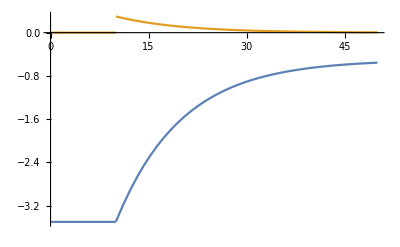

```mathematica
tstr=10;
aa=3;
τ=10;
bb=0.5;
Plot[{F[x,tstr,aa,τ,bb],dF[x,tstr,aa,τ,bb]},{x,0,50}]
```